```mathematica
SetDirectory @ NotebookDirectory[];
<<Rotation.m
<<Linearize.m
<<PlotCustom.m
<<NotationRules.m
```

## CINEMÁTICA

-Graphics-

### COORDENADAS GENERALIZADAS E QUASI-VELOCIDADES

```mathematica
𝕢[t_] = {x[t], y[t], ψ[t], ϕ[t], θ[t]};
𝕧[t_] = {Subscript[ω, 1][t], Subscript[ω, 2][t], Subscript[ω, 3][t]};
```

### MATRIZES DE ROTAÇÃO (N ↔ E)

```mathematica
Subscript[ℝ, "E"]^("N") = Rotation["z", "x"][ψ[t], ϕ[t]];
Subscript[ℝ, "N"]^("E") = Transpose[Subscript[ℝ, "E"]^("N")];
```

### POSIÇÃO DO CENTRO DE MASSA

```mathematica
Subscript[p, "C/O"]^("N") = {x[t], y[t], 0}; 
Subscript[p, "G/C"]^("E") = {0, 0, -r};
Subscript[p, "G/O"]^("N") = Subscript[ℝ, "E"]^("N").Subscript[p, "G/C"]^("E") + Subscript[p, "C/O"]^("N")
```

{-r Sin[ϕ[t]] Sin[ψ[t]]+x[t],r Cos[ψ[t]] Sin[ϕ[t]]+y[t],-r Cos[ϕ[t]]}

### VELOCIDADES ANGULARES

```mathematica
Subscript[ω, "a"]^("E") = Subscript[ℝ, "N"]^("E").{0, 0, ψ'[t]} + {ϕ'[t], 0, 0}
Subscript[ω, "r"]^("E")= {0, θ'[t], 0}
ω^("E") = 𝕧[t]
```

{ϕ'[t],Sin[ϕ[t]] ψ'[t],Cos[ϕ[t]] ψ'[t]}

{0,θ'[t],0}

{ω_1[t],ω_2[t],ω_3[t]}

### VELOCIDADE DO CENTRO DE MASSA

```mathematica
Subscript[v, "G"]^("N") = D[Subscript[p, "G/O"]^("N"),t] // FullSimplify
Subscript[v, "G"]^("E") = ω^("E")×(Subscript[p, "G/C"]^("E")) // FullSimplify
```

{x'[t]-r (Cos[ϕ[t]] Sin[ψ[t]] ϕ'[t]+Cos[ψ[t]] Sin[ϕ[t]] ψ'[t]),y'[t]+r Cos[ϕ[t]] Cos[ψ[t]] ϕ'[t]-r Sin[ϕ[t]] Sin[ψ[t]] ψ'[t],r Sin[ϕ[t]] ϕ'[t]}

{-r ω_2[t],r ω_1[t],0}

### EQUAÇÕES CINEMÁTICAS

```mathematica
ce = Solve[{Subscript[v, "G"]^("N") == Subscript[ℝ, "E"]^("N").Subscript[v, "G"]^("E"), ω^("E") == Subscript[ω, "a"]^("E") + Subscript[ω, "r"]^("E")}, 𝕢'[t]] // First // FullSimplify
```

{x'[t]→r Cos[ψ[t]] (-ω_2[t]+Tan[ϕ[t]] ω_3[t]),y'[t]→r Sin[ψ[t]] (-ω_2[t]+Tan[ϕ[t]] ω_3[t]),ψ'[t]→Sec[ϕ[t]] ω_3[t],ϕ'[t]→ω_1[t],θ'[t]→ω_2[t]-Tan[ϕ[t]] ω_3[t]}

### VELOCIDADE DO PONTO C

```mathematica
Subscript[v, "C"]^("N") = {x'[t], y'[t], 0} /. ce
Subscript[v, "C"]^("E") = Subscript[ℝ, "N"]^("E") . Subscript[v, "C"]^("N") // FullSimplify
```

{r Cos[ψ[t]] (-ω_2[t]+Tan[ϕ[t]] ω_3[t]),r Sin[ψ[t]] (-ω_2[t]+Tan[ϕ[t]] ω_3[t]),0}

{-r ω_2[t]+r Tan[ϕ[t]] ω_3[t],0,0}

## DINÂMICA

### TQMA – POLO C

```mathematica
Subscript[𝕀, "C"]^("E") = DiagonalMatrix[{i+1, j+1, i}] m r^2;
Subscript[H, "C"]^("E") = (Subscript[𝕀, "C"]^("E").ω^("E"));
D[Subscript[H, "C"]^("E"), t] + Subscript[ω, "a"]^("E")×Subscript[H, "C"]^("E") /. ce // FullSimplify
Subscript[M, "C"] = Subscript[p, "G/C"]^("E") ×(Subscript[ℝ, "N"]^("E").{0, 0, m g})
```

{m r^2 (-((1+j) ω_2[t] ω_3[t])+i Tan[ϕ[t]] ω_3[t]^2+(1+i) ω_1'[t]),m r^2 (ω_1[t] ω_3[t]+(1+j) ω_2'[t]),m r^2 (ω_1[t] ((1+j) ω_2[t]-(1+i) Tan[ϕ[t]] ω_3[t])+i ω_3'[t])}

{g m r Sin[ϕ[t]],0,0}

```mathematica
TQMA = (D[Subscript[H, "C"]^("E"), t] + Subscript[ω, "a"]^("E")×Subscript[H, "C"]^("E") + Subscript[v, "C"]^("E")×(m Subscript[v, "G"]^("E")) - Subscript[M, "C"]) /.ce // FullSimplify;
TQMA /. notation // TableForm
```

m r ((1+i) r OverDot[ω_1]-g s_ϕ+r ω_3 (-((1+j) ω_2)+(i s_ϕ ω_3)/c_ϕ))
m r^2 ((1+j) OverDot[ω_2]+ω_1 ω_3)
m r^2 (i OverDot[ω_3]+ω_1 (j ω_2-(i s_ϕ ω_3)/c_ϕ))

### EQUAÇÕES DIFERENCIAIS DE MOVIMENTO

```mathematica
{m𝔽, 𝕄} = Normal @ CoefficientArrays[TQMA, 𝕧'[t]];
𝕄 // MatrixForm
```

((1+i) m r^2 | 0 | 0
0 | (1+j) m r^2 | 0
0 | 0 | i m r^2)

```mathematica
𝔽 = -m𝔽 // FullSimplify;
𝔽 // MatrixForm
```

(m r (g Sin[ϕ[t]]+r ω_3[t] ((1+j) ω_2[t]-i Tan[ϕ[t]] ω_3[t]))
-m r^2 ω_1[t] ω_3[t]
m r^2 ω_1[t] (-j ω_2[t]+i Tan[ϕ[t]] ω_3[t]))

```mathematica
EOMa[t_] = Flatten @ Solve[
	(# == 0)& /@ TQMA,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;
EOMa[t] // TableForm
```

ω_1'[t]→(g Sin[ϕ[t]])/(r+i r)+((1+j) ω_2[t] ω_3[t])/(1+i)-(i Tan[ϕ[t]] ω_3[t]^2)/(1+i)
ω_2'[t]→-(ω_1[t] ω_3[t])/(1+j)
ω_3'[t]→ω_1[t] (-(j ω_2[t])/i+Tan[ϕ[t]] ω_3[t])

```mathematica
EOMa[t] /. notation // FullSimplify // TableForm
```

OverDot[ω_1]→(-i r s_ϕ ω_3^2+c_ϕ (g s_ϕ+(1+j) r ω_2 ω_3))/((1+i) r c_ϕ)
OverDot[ω_2]→-(ω_1 ω_3)/(1+j)
OverDot[ω_3]→ω_1 (-(j ω_2)/i+(s_ϕ ω_3)/c_ϕ)

## FORMA DE ESPAÇO DE ESTADOS

```mathematica
𝕩[t_] = {ϕ[t], Subscript[ω, 1][t], Subscript[ω, 2][t], Subscript[ω, 3][t]};
𝕗 = (𝕩'[t]/.ce/.EOMa[t]);
𝕗 // TableForm
```

ω_1[t]
(g Sin[ϕ[t]])/(r+i r)+((1+j) ω_2[t] ω_3[t])/(1+i)-(i Tan[ϕ[t]] ω_3[t]^2)/(1+i)
-(ω_1[t] ω_3[t])/(1+j)
ω_1[t] (-(j ω_2[t])/i+Tan[ϕ[t]] ω_3[t])

```mathematica
Eigenvalues[({{0, 1, 0, 0}, {Subscript[A, 21], 0, Subscript[A, 23], Subscript[A, 24]}, {0, Subscript[A, 34], 0, 0}, {0, Subscript[A, 42], 0, 0}})]
```

{0,0,-√(A_21+A_23 A_34+A_24 A_42),√(A_21+A_23 A_34+A_24 A_42)}

```mathematica
CharacteristicPolynomial[({{0, 1, 0, 0}, {Subscript[A, 21], 0, Subscript[A, 23], Subscript[A, 24]}, {0, Subscript[A, 34], 0, 0}, {0, Subscript[A, 42], 0, 0}}), s]//FullSimplify
```

s^2 (s^2-A_21-A_23 A_34-A_24 A_42)

## SOLUÇÕES EM REGIME PERMANENTE

```mathematica
PAR = {i -> 1/4, j-> 1/2, Subscript[Ω, "p"]-> √33};
RPcond = Join[{Subscript[ω, 1]'[t] -> 0, Subscript[ω, 2]'[t] -> 0, Subscript[ω, 3]'[t] -> 0}, {Subscript[ω, 1][t] -> 0, Subscript[ω, 2][t] -> Subscript[Ω, 2], Subscript[ω, 3][t] -> Subscript[Ω, 3], ϕ[t] -> Φ, g -> r Subscript[Ω, "p"]^2}]
TQMA/. RPcond
```

{ω_1'[t]→0,ω_2'[t]→0,ω_3'[t]→0,ω_1[t]→0,ω_2[t]→Ω_2,ω_3[t]→Ω_3,ϕ[t]→Φ,g→r Ω_p^2}

{m r (-r Sin[Φ] Ω_p^2+r Ω_3 (-((1+j) Ω_2)+i Ω_3 Tan[Φ])),0,0}

### TIPO I: Ω_3 ≠0

```mathematica
RP1 = Solve[(# == 0)& /@ (TQMA/. RPcond), {Subscript[Ω, 2]}] //First //FullSimplify
```

{Ω_2→((i Ω_3^2-Cos[Φ] Ω_p^2) Tan[Φ])/((1+j) Ω_3)}

#### LINEARIZAÇÃO

```mathematica
TQMAL1 = Linearize[TQMA, RPcond] /. RP1 //Simplify;
```

```mathematica
EOML1[t_] = Flatten @ Solve[
	(# == 0)& /@ TQMAL1,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;
EOML1[t] // TableForm
```

ω_1'[t]→(Cos[Φ] (-i Sec[Φ]^3 Ω_3^2+Ω_p^2) ϕ[t])/(1+i)+((1+j) Ω_3 ω_2[t])/(1+i)-(Sin[Φ] (i Sec[Φ] Ω_3^2+Ω_p^2) ω_3[t])/((1+i) Ω_3)
ω_2'[t]→-(Ω_3 ω_1[t])/(1+j)
ω_3'[t]→((j Sin[Φ] Ω_p^2+i Ω_3^2 Tan[Φ]) ω_1[t])/(i Ω_3+i j Ω_3)

#### MATRIZ DE ESTADOS 𝔸

```mathematica
𝔸1 = CoefficientArrays[𝕩'[t]/. ce /.EOML1[t], 𝕩[t]][[2]] // Normal;
𝔸1 //FullSimplify // MatrixForm
```

(0 | 1 | 0 | 0
(Cos[Φ] (-i Sec[Φ]^3 Ω_3^2+Ω_p^2))/(1+i) | 0 | ((1+j) Ω_3)/(1+i) | -(Sin[Φ] (i Sec[Φ] Ω_3^2+Ω_p^2))/((1+i) Ω_3)
0 | -Ω_3/(1+j) | 0 | 0
0 | (j Sin[Φ] Ω_p^2+i Ω_3^2 Tan[Φ])/(i Ω_3+i j Ω_3) | 0 | 0)

#### ANÁLISE DE ESTABILIDADE DE SOLUÇÕES

```mathematica
𝔸1 /. PAR //MatrixForm
```

(0 | 1 | 0 | 0
4/5 Cos[Φ] (33-1/4 Sec[Φ]^3 Ω_3^2) | 0 | (6 Ω_3)/5 | -(4 Sin[Φ] (33+1/4 Sec[Φ] Ω_3^2))/(5 Ω_3)
0 | -(2 Ω_3)/3 | 0 | 0
0 | (8 ((33 Sin[Φ])/2+1/4 Ω_3^2 Tan[Φ]))/(3 Ω_3) | 0 | 0)

```mathematica
Eigenvalues[𝔸1 /. PAR]//TableForm
```

0
0
-(ⅈ Sec[Φ]^4 √(30492+30492 Cos[2 Φ]-17424 Cos[4 Φ]-28314 Cos[6 Φ]-13068 Cos[8 Φ]-2178 Cos[10 Φ]-11088 Cos[Φ] Ω_3^2-8316 Cos[3 Φ] Ω_3^2-4356 Cos[5 Φ] Ω_3^2-1386 Cos[7 Φ] Ω_3^2-198 Cos[9 Φ] Ω_3^2+275 Ω_3^4+430 Cos[2 Φ] Ω_3^4+200 Cos[4 Φ] Ω_3^4+50 Cos[6 Φ] Ω_3^4+5 Cos[8 Φ] Ω_3^4))/(8 √15 Ω_3)
(ⅈ Sec[Φ]^4 √(30492+30492 Cos[2 Φ]-17424 Cos[4 Φ]-28314 Cos[6 Φ]-13068 Cos[8 Φ]-2178 Cos[10 Φ]-11088 Cos[Φ] Ω_3^2-8316 Cos[3 Φ] Ω_3^2-4356 Cos[5 Φ] Ω_3^2-1386 Cos[7 Φ] Ω_3^2-198 Cos[9 Φ] Ω_3^2+275 Ω_3^4+430 Cos[2 Φ] Ω_3^4+200 Cos[4 Φ] Ω_3^4+50 Cos[6 Φ] Ω_3^4+5 Cos[8 Φ] Ω_3^4))/(8 √15 Ω_3)

```mathematica
EIG1[deg_]:= {{Show[
	Plot[
		Sort@(Re/@Eigenvalues[𝔸1 /. PAR /.{Φ-> deg π/180, Subscript[Ω, 3]-> yr}]), {yr,0,10}, PlotRange->{-20,+20}, 
		PlotStyle->Cool⟦1⟧, GridLines->Automatic, Frame->True, FrameLabel->{"Ω_3 (rad/s)",None},
		PlotLabel->"Eigenvalues of disc model (Φ = "<>ToString[deg]<>".ba)",
		PlotLegends->Placed[LineLegend[{"Re (rad/s)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Roboto",FontSize->16}], Before],
		ImageSize->{450,450},
		AspectRatio->1
		],
	Plot[
		Sort@(*RedundantElim@*)Chop@(Im/@Eigenvalues[𝔸1 /. PAR /.{Φ-> deg π/180, Subscript[Ω, 3]-> yr}]),{yr,0,10}, 
		PlotStyle->{Cool⟦3⟧,Dashed},
		PlotLegends-> Placed[LineLegend[{"Im (rad/s)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Roboto",FontSize->16}],Before]
		]
	]},
	{Plot[
		Subscript[Ω, 2]/.RP1 //.PAR /.{Φ-> deg π/180, Subscript[Ω, 3]-> yr}, {yr,0.1,10}, PlotRange->All, 
		PlotStyle->Cool⟦5⟧, GridLines->Automatic, Frame->True, FrameLabel->{"Ω_3 (rad/s)",None},
		PlotLabel->"Steady state value of Ω_2 (Φ = "<>ToString[deg]<>".ba)",
		PlotLegends->Placed[LineLegend[{"Ω_2 (rad/s)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Roboto",FontSize->16}], Before],
		ImageSize->{450,450},
		AspectRatio->1
		]}}//TableForm
```

```mathematica
Manipulate[EIG1[ϕ],{ϕ,Range[0,50,2]},ControlType-> Setter]
```

### TIPO II: Ω_3 =0, Φ = 0

```mathematica
TQMA/. RPcond /.{Subscript[Ω, 3]->0}
```

{-m r^2 Sin[Φ] Ω_p^2,0,0}

```mathematica
RP2 = {Φ->0, Subscript[Ω, 3]->0};
```

#### LINEARIZAÇÃO

```mathematica
TQMAL2 = Linearize[TQMA, RPcond] /. RP2  //Simplify
```

{m r^2 (-Ω_p^2 ϕ[t]-(1+j) Ω_2 ω_3[t]+(1+i) ω_1'[t]),(1+j) m r^2 ω_2'[t],m r^2 (j Ω_2 ω_1[t]+i ω_3'[t])}

```mathematica
EOML2[t_] = Flatten @ Solve[
	(# == 0)& /@ TQMAL2,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;
EOML2[t] // TableForm
```

ω_1'[t]→(Ω_p^2 ϕ[t])/(1+i)+((1+j) Ω_2 ω_3[t])/(1+i)
ω_2'[t]→0
ω_3'[t]→-(j Ω_2 ω_1[t])/i

#### MATRIZ DE ESTADOS 𝔸

```mathematica
𝔸2 = CoefficientArrays[𝕩'[t]/. ce /.EOML2[t], 𝕩[t]][[2]] // Normal;
𝔸2 // MatrixForm
```

(0 | 1 | 0 | 0
Ω_p^2/(1+i) | 0 | 0 | ((1+j) Ω_2)/(1+i)
0 | 0 | 0 | 0
0 | -(j Ω_2)/i | 0 | 0)

#### ANÁLISE DE ESTABILIDADE DE SOLUÇÕES

```mathematica
𝔸2 /. PAR //MatrixForm
```

(0 | 1 | 0 | 0
132/5 | 0 | 0 | (6 Ω_2)/5
0 | 0 | 0 | 0
0 | -2 Ω_2 | 0 | 0)

```mathematica
Eigenvalues[𝔸2 /. PAR]//TableForm
```

0
0
-2 √(3/5) √(11-Ω_2^2)
2 √(3/5) √(11-Ω_2^2)

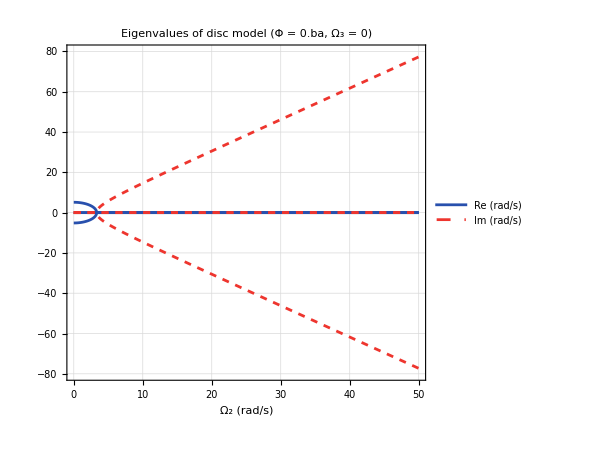

```mathematica
EIG2 = Show[
	Plot[
		Sort@(Re/@Eigenvalues[𝔸2 /. PAR /.{Subscript[Ω, 2]-> yr}]), {yr,0,50}, PlotRange->{-80,+80}, 
		PlotStyle->Cool⟦1⟧, GridLines->Automatic, Frame->True, FrameLabel->{"Ω_2 (rad/s)",None},
		PlotLabel->"Eigenvalues of disc model (Φ = 0.ba, Ω_3 = 0)",
		PlotLegends->Placed[LineLegend[{"Re (rad/s)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Roboto",FontSize->16}], Before],
		ImageSize->{450,450},
		AspectRatio->1
		],
	Plot[
		Sort@(*RedundantElim@*)Chop@(Im/@Eigenvalues[𝔸2 /. PAR /.{Subscript[Ω, 2]-> yr}]),{yr,0,50}, 
		PlotStyle->{Cool⟦3⟧,Dashed},
		PlotLegends-> Placed[LineLegend[{"Im (rad/s)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Roboto",FontSize->16}],Before]
		]
	]
```

## EXPORT TO OCTAVE

### RULES

```mathematica
Unprotect[Power];
Format[Power[a_,n_Integer],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];
```

```mathematica
crule = MapThread[#1->#2&, {#, x/@((Range[Length@#]))}& @ 𝕩[t]];
csorule = {"Cos"->"cos", "Sin"->"sin", "Tan"->"tan", "Sec"->"sec"};
csqrule = {};
```

### EXPORT FILE

```mathematica
fileD = OpenWrite["export/disc_OCT.m"];
(*WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["dy(``) = ``;", ii, (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕪'[t]/.EOM[t])], -1]));*)
WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["    ``;", (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕩'[t]/.ce/.EOMa[t](*Join[𝕣𝕢[t], EOM2[t]]*)/.PAR)], -1]));
WriteString[fileD, "\n"];
Close[fileD];
```